```mathematica
=Transpose[Transpose[widthtable][[2]]][[3]]
```

{0.24831,0.26762,0.308312,0.360112,0.417136,0.484905,0.557552,0.634546,0.721508,0.795433}

```mathematica
beads=Transpose[Transpose[widthtable][[1]]][[2]]
```

{1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}

```mathematica
ch2measure=Transpose[Transpose[widthtable][[2]]][[3]]
```

{0.245901,0.264688,0.306629,0.358912,0.416515,0.484619,0.55745,0.63455,0.721498,0.795493}

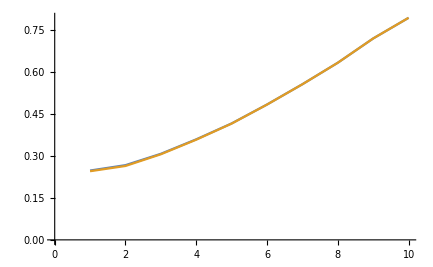

```mathematica
ListLinePlot[{ch1measure,ch2measure}]
```

```mathematica
Export["2channelscomparasion.csv",{N[beads],ch1measure,ch2measure}*1000]
```

2channelscomparasion.csv

```mathematica
SystemOpen["2channelscomparasion.csv"]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["2channelscomparasion.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["2channelscomparasion.csv"]]]
```

```mathematica
bead100image1=-Graphics-;
```

```mathematica
bead100image2=-Graphics-;
```

```mathematica
imgdata1=Flatten[Table[{i,j,ImageData[bead100image1][[i,j]]},{i,Length[ImageData[bead100image1]]},{j,Length[ImageData[bead100image1][[i]]]}],1];
```

```mathematica
imgdata2=Flatten[Table[{i,j,ImageData[bead100image2][[i,j]]},{i,Length[ImageData[bead100image2]]},{j,Length[ImageData[bead100image2][[i]]]}],1];
```

```mathematica
gaussianmodel=a Exp[-b ((x-x00)^2+(y-y00)^2)]+c;
```

```mathematica
fit1=FindFit[imgdata1,gaussianmodel,{a,b,{c,0},{x00,ImageDimensions[bead100image1][[1]]/2},{y00,ImageDimensions[bead100image1][[2]]/2}},{x,y}]
```

{a→0.00343027,b→0.114284,c→0.0031808,x00→32.5149,y00→32.7922}

```mathematica
fit2=FindFit[imgdata2,gaussianmodel,{a,b,{c,0},{x00,ImageDimensions[bead100image2][[1]]/2},{y00,ImageDimensions[bead100image2][[2]]/2}},{x,y}]
```

{a→0.00594537,b→0.117141,c→0.00387444,x00→32.6225,y00→30.7759}

```mathematica
convolintensityfunc1[d_]:=Table[NIntegrate[discgeneratorfunc[d,x,y]*(ⅇ^(-b ((x0-x)^2+(y0-y)^2))/.fit1),{x,-Infinity,Infinity},{y,-Infinity,Infinity}],{x0,-50,50},{y0,-50,50}]
```

```mathematica
convolintensityfunc2[d_]:=Table[NIntegrate[discgeneratorfunc[d,x,y]*(ⅇ^(-b ((x0-x)^2+(y0-y)^2))/.fit2),{x,-Infinity,Infinity},{y,-Infinity,Infinity}],{x0,-50,50},{y0,-50,50}]
```

```mathematica
cov200a1=convolintensityfunc1[0.2];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
cov200a2=convolintensityfunc2[0.2]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{6.00941×10^-241,4.63774×10^-236,2.84213×10^-231,1.38322×10^-226,94,2.84213×10^-231,4.63774×10^-236,6.00941×10^-241},99,{1}}
 |  |  |  |

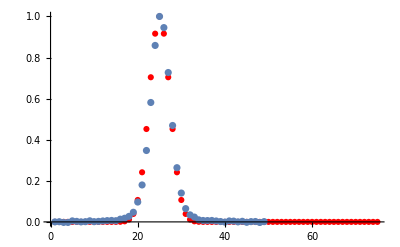

```mathematica
Show[ListPlot[Drop[Total[cov200a1]/Max[Total[cov200a1]],26],PlotRange->All,PlotStyle->Red],ListPlot[(real-real[[1]])/Max[real-real[[1]]],PlotRange->All]]
```

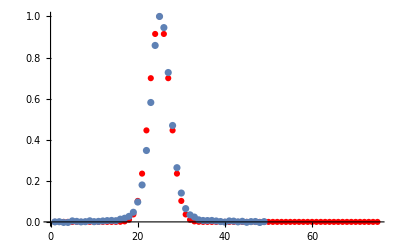

```mathematica
Show[ListPlot[Drop[Total[cov200a2]/Max[Total[cov200a2]],26],PlotRange->All,PlotStyle->Red],ListPlot[(real-real[[1]])/Max[real-real[[1]]],PlotRange->All]]
```

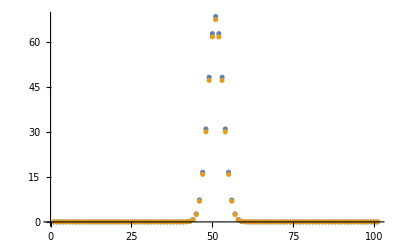

```mathematica
ListPlot[{Total[cov200a1],Total[cov200a2]},PlotRange->All]
```

```mathematica
ListPlot[{imgdata1,imgdata2}]
```

-Graphics-

```mathematica
imgdata1
```

{{1,1,0.00341802},{1,2,0.00334173},{1,3,0.00308232},4090,{64,62,0.00308232},{64,63,0.00314336},{64,64,0.00317388}}
 |  |  |  |

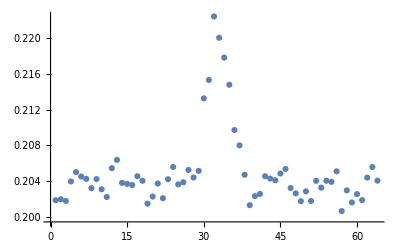

```mathematica
ListPlot[Total[ImageData[bead100image1]],PlotRange->All]
```

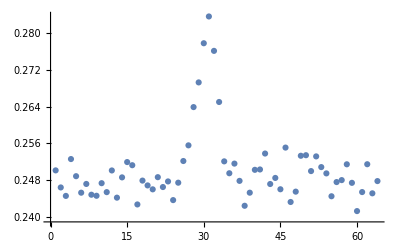

```mathematica
ListPlot[Total[ImageData[bead100image2]],PlotRange->All]
```

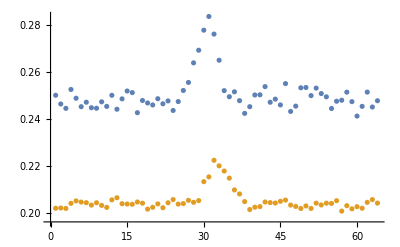

```mathematica
ListPlot[{Total[ImageData[bead100image2]],Total[ImageData[bead100image1]]},PlotRange->All]
```